### Specific to the case of trefoil, for which the following f_n’s are defined

```mathematica
f=<||>;
```

```mathematica
f[1]=1;
f[3]=2;
f[5]=1/q+3+q;
f[7]=2/q^2+2/q+5+2 q+2 q^2;
f[9]=1/q^4+3/q^3+4/q^2+5/q+8+5 q+4 q^2+3 q^3+q^4;
f[11]=2/q^6+2/q^5+6/q^4+7/q^3+10/q^2+10/q+15+10 q+10 q^2+7 q^3+6 q^4+2 q^5+2 q^6;
f[13]=1/q^9+3/q^8+4/q^7+7/q^6+11/q^5+15/q^4+18/q^3+21/q^2+23/q+27+23 q+21 q^2+18 q^3+15 q^4+11 q^5+7 q^6+4 q^7+3 q^8-3 q^8+q^9;
```

```mathematica
Do[f[n+14]=Simplify[-q^(-n/2-11/2)/(q^(n/2+13/2)-1)*(f[n] (q^(n/2+17/2)-q^(n+9))+f[n+2] (q^(n/2+15/2)-q^(n/2+17/2)+q^(n+9)-q^(n+10))+f[n+4] (-q^(n/2+11/2)-q^(n/2+17/2)-q^(n/2+19/2)+q^(3 n/2+21/2)+q^(n+8)+q^(n+9)+q^(n+12))+f[n+6] (-q^(n/2+9/2)+q^(n/2+11/2)-q^(n/2+15/2)-q^(n/2+17/2)+q^(3 n/2+25/2)+q^(n+9)+q^(n+10)-q^(n+12)+q^(n+13))+f[n+8] (q^(n/2+11/2)+q^(n/2+13/2)-q^(n/2+17/2)+q^(n/2+19/2)-q^(3 n/2+31/2)-q^(n+8)-q^(n+9)+q^(n+11)-q^(n+12))+f[n+10] (q^(n/2+9/2)+q^(n/2+11/2)+q^(n/2+17/2)-q^(3 n/2+35/2)-q^(n+9)-q^(n+12)-q^(n+13))+f[n+12] (q^(n/2+11/2)-q^(n/2+13/2)+q^(n+11)-q^(n+12))-f[n+4] q^7-f[n+6] q^5+f[n+8] q^2+f[n+10])];
,{n,1,50,2}]
```

```mathematica
u[r_,m_]:={1/2(1/r+m),1/2(-1/r+m),-1/2(1/r+m),1/2(1/r-m)}
```

```mathematica
xpref[m_,p_,r_,a_]:=Simplify[Sum[(-1)^(n-1)(Boole[IntegerQ[(r u[r,m][[n]]-a)/p]]q^(-u[r,m][[n]]^2 r/p)),{n,1,4}]]
```

```mathematica
pf[p_,r_,a_,trunc_]:=Series[Sum[xpref[m,p,r,a]f[m],{m,1,30,2}],{q,0,trunc}]
```

```mathematica
-pf[-1,2,0,30]/q^(4/5)/2
```

0

```mathematica
pf3[p_,r_,a_,trunc_]:=Series[Sum[xpref[m,p,r,a]f3[m],{m,1,50,2}],{q,0,trunc}]
```

```mathematica
f3[m_]:=q^((m^2-1)/24)
```

### Trefoil p=-1, a=0, various r

```mathematica
-pf3[-1,1,0,50]/2
```

1-q+q^(4/3)-q^(13/3)+q^5-q^10+q^11-q^18+q^(58/3)-q^(85/3)+q^30-q^41+q^43+O[q]^(151/3)

### Try p=-1, r=2, a=0

```mathematica
-pf[-1,2,1/2,30]/q^(1/8)/2
```

1-q+2 q^3-2 q^6+q^9+3 q^10+q^11-q^14-3 q^15-q^16+2 q^19+2 q^20+5 q^21+2 q^22+2 q^23-2 q^26-2 q^27-5 q^28-2 q^29+O[q]^30

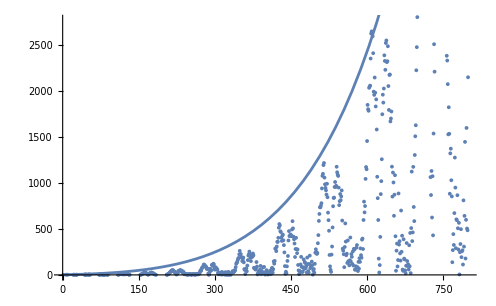

```mathematica
trunc=800;
data4=-pf[-1,4,1/2,trunc]/2/q^(9/16);
list4=Exponent[data4,q,List];
(*ListPlot[Table[list4[[i+1]]-list4[[i]],{i,1,Length[list4]-1}]]*)
coef4=Table[Coefficient[data4,q^(list4[[n]])],{n,2,Length[list4]}];
coef4p=Table[Abs[Coefficient[data4,q^(list4[[n]])]],{n,2,Length[list4]}];
Show[ListPlot[Transpose[{Rest[list4],coef4p}]],Plot[E^(2/(2 Pi)Sqrt[x]),{x,0,trunc}]]
```

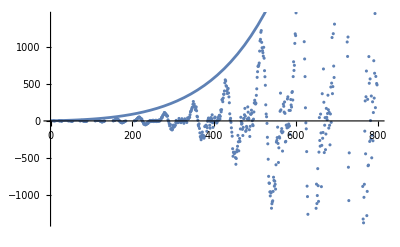

```mathematica
Show[ListPlot[Transpose[{Rest[list4],coef4}]],Plot[E^(2/(2 Pi)Sqrt[x]),{x,0,trunc}]]
```

```mathematica
coef4
```

{1,2,2,1,3,1,1,3,1,2,2,5,2,2,2,2,5,2,2,1,3,4,5,8,5,4,3,1,1,3,4,5,8,5,4,3,1,2,2,6,7,10,10,15,10,10,7,6,6,7,10,10,15,10,10,7,6,2,2,1,3,4,7,11,15,18,21,23,27,23,21,18,14,8,3,3,11,14,18,21,23,27,23,21,18,15,11,7,4,1,2,2,6,8,13,16,26,29,38,41,48,48,54,42,42,35,28,23,26,5,6,15,25,44,39,40,49,54,39,44,45,30,21,35,18,7,13,12,6,6,9,1,3,5,6,8,8,9,1,3,5,6,8,8,9,1,3,5,6,9,11,5,8,16,12,19,41,51,45,68,80,83,91,112,112,100,93,94,82,65,70,66,15,1,8,37,67,46,52,109,109,100,122,114,81,57,84,79,72,64,57,23,7,7,17,24,12,22,3,33,9,6,12,17,23,2,30,10,5,2,12,32,1,28,7,6,1,21,41,24,33,36,52,49,84,120,131,140,161,180,184,224,262,221,228,191,192,150,163,189,137,63,54,9,54,72,39,102,161,211,225,254,228,186,150,191,218,198,233,213,77,71,74,58,70,140,91,6,18,39,26,18,59,98,10,45,14,28,82,24,87,18,4,9,39,52,6,10,5,28,19,8,45,30,11,70,77,25,61,147,122,152,286,288,259,309,360,361,404,514,554,539,475,467,405,370,428,439,377,324,245,96,12,35,19,93,152,206,375,477,423,424,441,433,422,495,585,507,417,388,342,195,282,404,280,237,277,108,49,8,44,32,114,197,87,32,34,83,169,64,141,130,74,96,26,189,118,41,23,119,210,73,91,90,145,106,3,50,64,24,121,242,279,250,228,238,345,433,588,664,737,736,755,781,942,1079,1101,1196,1219,1060,987,948,921,875,993,846,678,596,481,217,93,56,33,221,309,517,748,838,842,958,1012,957,971,1178,1118,1092,1078,951,760,803,881,814,855,920,592,286,264,225,84,304,561,363,214,231,130,375,149,141,104,160,407,146,227,197,119,256,102,284,276,58,57,94,296,325,85,42,142,68,182,142,289,215,187,384,396,282,598,798,681,750,1046,1175,1151,1458,1852,1805,1788,2038,2051,2062,2357,2629,2653,2641,2599,2415,1996,1961,2150,1985,1835,1912,1584,1069,836,598,177,26,107,414,880,1021,1260,1750,1963,1877,2030,2392,2331,2234,2526,2554,2318,2328,2491,2057,1797,2178,2183,1672,1704,1780,1179,853,1115,1007,644,874,1086,421,45,264,341,92,162,887,330,367,234,156,701,252,427,58,44,388,177,169,49,17,100,347,151,97,116,59,323,94,457,19,510,1125,368,463,1177,740,586,1306,1510,1630,2229,2481,2808,3133,3059,3368,3742,3612,4288,4888,4783,5196,5836,5157,5487,6375,5736,5392,5780,5139,4575,4517,4331,4415,4175,3263,3672,3011,1065,870,1132,625,1075,431,1540,2513,2214,3271,4155,4215,4878,5157,5053,5426,5122,5398,5864,5203,5107,6127,5065,4077,5345,5078,3691,4551,4635,3286,2943,2989,2387,2335,2078,1531,1826,1537,884,1324,1375,1031,855,138,270,444,326,673,1278,951,291,605,596,868,508,277,567,5,247,336,498,193,258,268,113,812,308,643,1449,179,600,1601,505,486,2153,2611,2053,3028,3881,4366,3975,3568,5756,6277,4764,7254,9889,8090,8325,10822,9782,9523,11624,11554,11894,13430,13200,12889,13854,13363,12329,12479,11733,11645,10848,9406,10226,10161,7569,7496,7688,4636,3105,2911,650,491,790,3188,3590,3399,6918,7780,6752,9135,10662,10194,11242,12244,12607,13560,12554,11437,13553,12405,10001,12220,13218,11162,11741,12328,10459,9978,8480,6920,8001,6998,5311,6380,6527,4674,4980,4293,2869,4176,2576,332,2255,1890,414,1022,2518,1467,1384,1215,378,492,1346,2024,734,475,1318,1497,2961,588,643,1113,480,1007,406,1014,464,294,207,878,1456,731,865,831,1341,365,1451,2058,1997,1321,1829,1330,2214,1277,801,1024,341,1244,94,55,134,369,14,593,106,1255,448,718,211,1350,1013,3141,1361,2010,1773,483,2760,1176,2114,1182,128,940,176,1084,731,1867,682,1583,45,976,1195,337,1624,869,611,1628,272,2222,719,2329,1355,1207,1996,779,2103,1203,1904,268,2229,560,2610,981,1410,2804,371,2770,869,427,1867,515,2158,844,312,1736,50,1939,89,1938,1756,2466,1736,1165,2421,1179,4595,882,2785,1154,434,3900,94,3230,407,82,2203,229,1764,310,979,2074,1011,1843,25,2512,1192,4019,1541,1954,2704,196,4317,134,3527,1737,2136,2500,1925,1651,421,2790,708,2992,186,962,2187,9,4069,1026,2092,2832,914,3667,24,3952,2366,3460,2298,1115,2958,945,5093,956,3078,1688,879,3893,1426,4164,203,2676,2316,1378,2907,773,3270,2502,1139,2834,1285,4180,1197,4210,1907,1964,3634,1225,4213,139,3889,2314,2883,2994,1403,3310,418,4195,2197,3004,2572,374,3100,1608,3976,2104,1787,1986,456,4026,409,5251,1840,3271,3940,1932,5080,226,5840,2685,4585,2253,1581,3972,39,6220,285,2958,2119,427,4640,816,4442,1625,2730,3877,1734,4615,664,6250,3441,4519,4109,676,5637,776,5844,2107,2696,3740,1740,4144,791,4185,2472,3697,2942,1280,3376,1902,5478,3104,3092,3498,827,5315,1750,5417,3083,2552,4142,627,4582,887,5957,2413,4705,2910,1677,5757,424,7221,999,3261,3716,716,5577,501,4933,3705,2842,4504,988,5096,1082,7271,2526,5226,3754,1967,7156,777,7981,2459,4304,5681,2190,6275,83,6151,3408,4669,3248,1614,3990,1170,6354,2592,3966,3401,465,5967,1127,7835,3740,4958,5575,1022,6957,1532,7373,3586,3678,3858,566,4790,229,6289,1584,4209,3016,988,5888,817,7152,3140,3186,5840,245,7141,1161,6330,4723,4130,5683,1710,5783,1058,7807,2645,5619,3495,2348,7177,1210,8805,2624,5448,6135,2402,6921,1677,7163,5175,4686,4523,493,6300,1506,8728,2795,5411,5477,2229,8594,66,9637,4072,6650,5644,2052,7292,1476,9087,3110,3917,3798,931,6279,748,6509,2682,3100,5570,2127,7223,48,8584,4825,6367,6203,1275,7492,2502,8845,4204,4362,5113,689,6820,314,7346,2487,5377,4460,3340,5941,546,8792,4903,6424,6209,390,8968,3158,10320,5105,5010,6629,900,8318,332,9052,3190,6681,5184,3526,8055,132,10939,3785,7254,6381,1486,9355,2024,9510,5098,3743,6640,144,8135,995,8660,3622,5676,6198,3318,8966,421,10790,4919,7373,7200,2238,8440,1761,9449,4725,4835,5075,260,6426,1215,7766,3527,4896,4882,1995,7683,955,11281,4834,7893,7204,1258,10757,2400,11314,5041,5138,6558,1346,7366,123,8762,3201,7098,4962,2685,8771,1038,12486,4499,6862,8535,832,12069,1675,10757,6896,5548,8864,1813,8336,2143,10130,4883,7948,5406,3377,10007,887,12802,3653,7463,8429,2327,9929,2417,9107,7687,5090,6916,215,7369,2732,10995,3841,7544,5101,2560,10258,526,12904,3856,7635,8226,2523,11039,1359,11039,5818,5473,6493,369,7611,1485,9613,3444,6026,5767,2305,10370,73,13311,5828,8632,10130,2464,12288,2513,12449,7215,6680,8116,1158,9137,1024,10774,3818,7575,6145,3594,9947,347,13276,6318,8837,9766,1438,12371,4208,13114,8265,6861,8532,655,9951,1862,11968,3891,7893,5907,3533,10736,979,13727,4363,8734,8951,2284,11749,2985,11911,7362,5543,7658,248,9164,1386,10781,3682,6794,7279,4405,11528,1310,14052,6516,10487,9712,3847,11614,2737,13764,6388,6878,6972,558,9965,1772,10895,4819,6413,8387,3864,11300,302,15135,7708,11768,10464,2150,13925,4699,15531,7643,6301,8948,350,11331,727,11980,4170,8139,7061,4195,10882,519,14842,6373,9427,10375,1187,14497,3390,14306,8277,6614,10428,1145,10715,1301,11804,4687,9166,6380,5290,11066,1132,15846,5344,10938,9704,2887,13011,3460,13458,8553,6353,8991,105,10321,2292,12809,5209,9089,7515,4338,12773,400,17213,5974,11261,10867,2765,15035,2996,15175,8493,6836,9841,204,10693,2313,12244,5517,8073,7906,3120,13332,670,17414,7345,10683,13008,2243,16647,3291,15722,9613,7589,10953,1587,10391,1469,12196,5123,9627,6331,4260,11648,714,17399,6452,11046,11562,1958,16144,3265,15608,8975,7846,10376,1451,10907,2378,14207,5121,10757,6403,4570,13476,1516,18660,4671,11323,11819,3427,15779,3063,14613,10635,6935,10911,186,11493,3550,14580,5675,9748,8641,4385,15200,806,18187,7726,11773,13566,3875,15738,3855,16210,10366,8263,10299,325,11532,3146,13511,6007,8284,8765,3986,13882,127,18887,8360,13670,13099,3100,17111,4926,18213,9499,8331,10417,218,12834,827,14592,4044,9735,8091,5342,13795,1183,18242,7036,12258,12826,2980,17123,4398,17920,10775,8931,11882,684,13381,1921,15365,4954,10589,8401,6214,14417,1731,18884,7691,13339,13330,3466,16583,5740,17623,11576,8244,11284,1075,13347,3559,15354,6496,9640,9828,4889,15325,16,20080,9010,14247,13850,3450,17860,4684,19026,9708,8026,10749,1182,13177,2249,14361,5829,8869,10087,5340,15426,820,20321,8846,14876,14354,4396,18807,4140,19758,10562,9259,12379,1117,13752,923,15220,5427,11641,8492,6547,14271,111,21191,8209,14254,13958,2127,19673,4966,19553,11554,8854,13690,975,14088,3072,16105,7046,11885,8301,5119,15716,271,22400,6720,13765,14163,2604,19564,4794,17959,12616,7343,13637,703,13592,3866,16225,7352,11533,10142,5634,17134,833,22276,8436,14608,15172,4398,19390,4020,19565,12009,9725,12850,765,13437,3206,16161,6931,11772,8940,5771,16123,363,23533,8525,15876,15923,3597,21874,4375,21488,11791,10131,13697,1656,14412,1696,16987,5957,12419,8745,5378,16398,38,22721,8461,14022,16442,2803,21867,4948,20477,13463,9242,14725,140,14644,3725,17130,7054,11930,9641,5831,17231,1222,22780,8524,15160,15796,4177,19542,5968,19776,13996,9682,13412,907,14899,4461,18624,6748,12292,10262,6040,18740,1507,24602,9156,16921,16643,5349,21352,4857,22496,12507,10920,13008,228,15655,2805,17972,6390,11027,11699,6154,18764,1313,23943,10537,17672,17603,5287,21916,5915,23207,13333,10627,14128,374,16045,2165,17607,6463,11949,10793,7223,17025,688,23270,10455,16179}

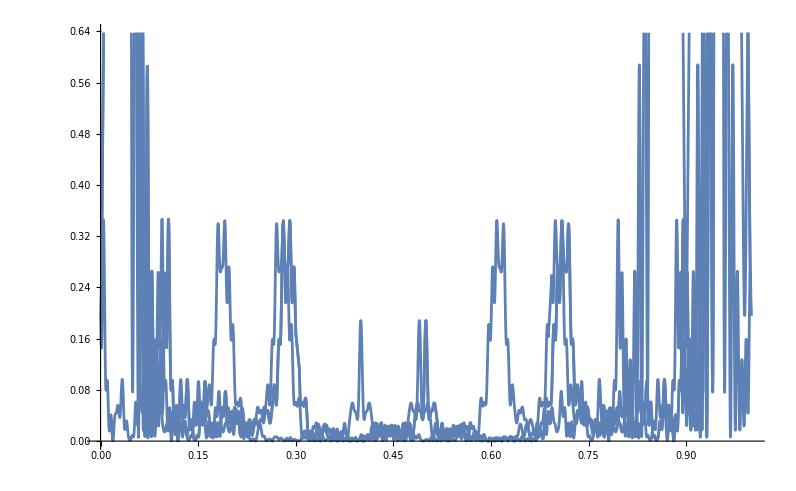

```mathematica
β={0,0.01,0.1,1};
Plot[Table[Norm[(z3/.q->E^(2 I Pi (t+β[[i]])))]^2/52039,{i,1,4}],{t,0,1}]
```

```mathematica
Plot[z3^2,{t,0,4}]
```

-Graphics-

```mathematica
list3=Exponent[%,q,List]
```

{0}

```mathematica
ListPlot[Table[Log[(list3[[i+1]]-list3[[i]])/(list3[[i]]-list3[[i-1]])],{i,2,Length[list3]-1}]]
```

-Graphics-

```mathematica
ListPlot[Table[list3[[i+1]]-list3[[i]],{i,1,Length[list3]-1}]]
```

-Graphics-

it seems like (r u - a)/p∈ℤ is never true where u = {1/2 (1/2+m),1/2 (-(1/2)+m), -1/2 (1/2+m),1/2 (1/2-m)}

```mathematica
uu = {1/2(1/r+m),1/2(-1/r+m),-1/2(1/r+m),1/2(1/r-m)};
```

```mathematica
Table[uu/.{r->2},{m,1,50}]
```

{{3/4,1/4,-3/4,-1/4},{5/4,3/4,-5/4,-3/4},{7/4,5/4,-7/4,-5/4},{9/4,7/4,-9/4,-7/4},{11/4,9/4,-11/4,-9/4},{13/4,11/4,-13/4,-11/4},{15/4,13/4,-15/4,-13/4},{17/4,15/4,-17/4,-15/4},{19/4,17/4,-19/4,-17/4},{21/4,19/4,-21/4,-19/4},{23/4,21/4,-23/4,-21/4},{25/4,23/4,-25/4,-23/4},{27/4,25/4,-27/4,-25/4},{29/4,27/4,-29/4,-27/4},{31/4,29/4,-31/4,-29/4},{33/4,31/4,-33/4,-31/4},{35/4,33/4,-35/4,-33/4},{37/4,35/4,-37/4,-35/4},{39/4,37/4,-39/4,-37/4},{41/4,39/4,-41/4,-39/4},{43/4,41/4,-43/4,-41/4},{45/4,43/4,-45/4,-43/4},{47/4,45/4,-47/4,-45/4},{49/4,47/4,-49/4,-47/4},{51/4,49/4,-51/4,-49/4},{53/4,51/4,-53/4,-51/4},{55/4,53/4,-55/4,-53/4},{57/4,55/4,-57/4,-55/4},{59/4,57/4,-59/4,-57/4},{61/4,59/4,-61/4,-59/4},{63/4,61/4,-63/4,-61/4},{65/4,63/4,-65/4,-63/4},{67/4,65/4,-67/4,-65/4},{69/4,67/4,-69/4,-67/4},{71/4,69/4,-71/4,-69/4},{73/4,71/4,-73/4,-71/4},{75/4,73/4,-75/4,-73/4},{77/4,75/4,-77/4,-75/4},{79/4,77/4,-79/4,-77/4},{81/4,79/4,-81/4,-79/4},{83/4,81/4,-83/4,-81/4},{85/4,83/4,-85/4,-83/4},{87/4,85/4,-87/4,-85/4},{89/4,87/4,-89/4,-87/4},{91/4,89/4,-91/4,-89/4},{93/4,91/4,-93/4,-91/4},{95/4,93/4,-95/4,-93/4},{97/4,95/4,-97/4,-95/4},{99/4,97/4,-99/4,-97/4},{101/4,99/4,-101/4,-99/4}}

When i turn p = -1/2, the result does look like something, however not found as any series in the paper

```mathematica
-pf[-1/2,2,0,40]q^(-1/4)/2
```

1-q^2+2 q^6-2 q^12+q^19+3 q^20+q^21-q^29-3 q^30-q^31+O[q]^40

```mathematica
Keys[f]
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63}